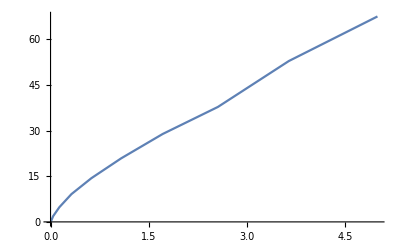

```mathematica
ListLinePlot[{{50000000,0.128843},{400000000,1.887671},{1350000000,4.829464},{3200000000,9.137533},{6250000000,14.371432},{10800000000,20.885905},{17150000000,28.891322},{25600000000,37.787749},{36450000000,52.877215},{50000000000,67.521850}}]
```

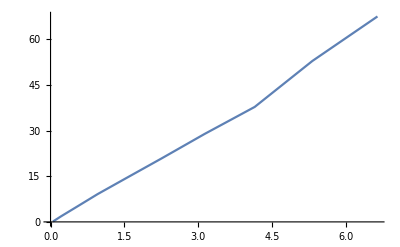

```mathematica
ListLinePlot[{{50000*N[Log2[1000]],0.128843},{200000*N[Log2[2000]],1.887671},{450000*N[Log2[3000]],4.829464},{800000*N[Log2[4000]],9.137533},{1250000*N[Log2[5000]],14.371432},{1800000*N[Log2[6000]],20.885905},{2450000*N[Log2[7000]],28.891322},{3200000*N[Log2[8000]],37.787749},{4050000*N[Log2[9000]],52.877215},{5000000*N[Log2[10000]],67.521850}}]
```

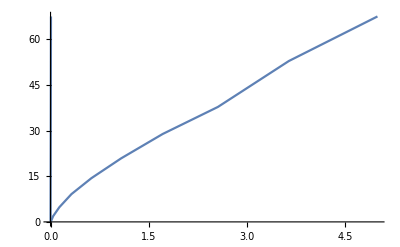

```mathematica
Show[%8,%9]
```

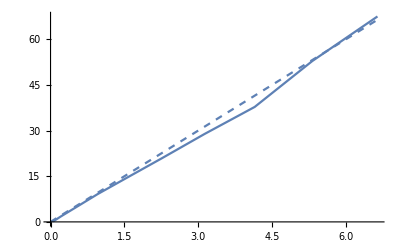

```mathematica
Show[%67,Plot[x/1000000,{x,0,5000000*N[Log2[10000]]},PlotStyle->Dashed]]
```

```mathematica
Format[edges,TraditionalForm]:="E"
```

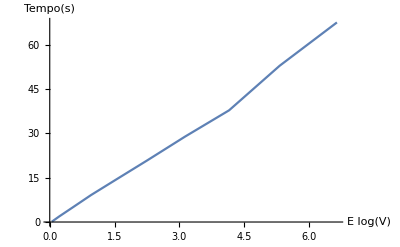

```mathematica
Show[%1,AxesLabel->{ToExpression["edges*Log[V]",TraditionalForm],HoldForm[Tempo[s]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

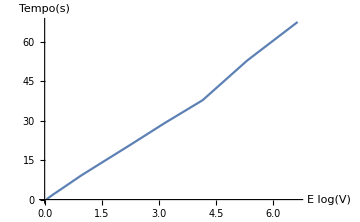

```mathematica
Show[%5,ImageSize->Medium]
```

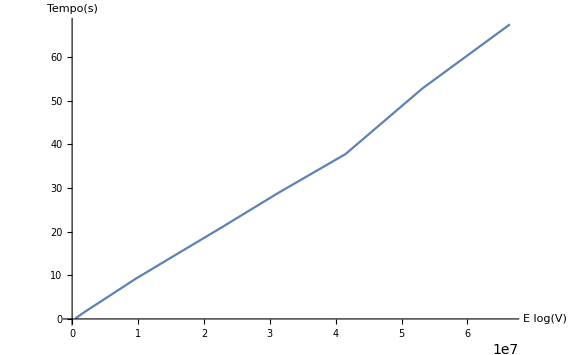

```mathematica
Show[%6,ImageSize->Large]
```